```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PP/west/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOWest.res
```

```mathematica
mc=1.3;mb=4.;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(15.1047)^2;mt=170;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137; nf=6;
```

```mathematica
R1
```

2.35588

```mathematica
(MC=1.3,MB=4,MT=170,alphaS=0.3,alpha=1/137,fBc=1,mu=2*(MC+MB))
```

```mathematica
Sqrt[4 m^2]
```

10.6

```mathematica
(2mc+2 mc)^2
```

27.04

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

-1.30331×10^-10 eps Aconj(1.3) AS^3-(3.00425×10^-13 Aconj(1.3) AS^3)/eps+4.77025×10^-11 Aconj(1.3) AS^3-1.66123×10^-11 eps Aconj(4.) AS^3+(9.76382×10^-14 Aconj(4.) AS^3)/eps-3.00713×10^-12 Aconj(4.) AS^3-1.5234×10^-12 eps Aconj(170.) AS^3+3.60789×10^-13 Aconj(170.) AS^3-1.70531×10^-10 eps Bconj(13.7265,0.,0.) AS^3-1.23072×10^-10 Bconj(13.7265,0.,0.) AS^3+2.31108×10^-11 eps Bconj(13.7265,1.3,1.3) AS^3+(3.05465×10^-12 Bconj(13.7265,1.3,1.3) AS^3)/eps-1.18983×10^-11 Bconj(13.7265,1.3,1.3) AS^3+3.37483×10^-11 eps Bconj(13.7265,4.,4.) AS^3-8.75732×10^-12 Bconj(13.7265,4.,4.) AS^3+3.32674×10^-8 eps Bconj(13.7265,170.,170.) AS^3-9.61485×10^-9 Bconj(13.7265,170.,170.) AS^3-1.30211×10^-9 eps Bconj(49.5253,1.3,4.) AS^3-(3.5819×10^-12 Bconj(49.5253,1.3,4.) AS^3)/eps+1.92556×10^-11 Bconj(49.5253,1.3,4.) AS^3+1.2974×10^-9 eps Bconj(49.5253,4.,1.3) AS^3-(3.5819×10^-12 Bconj(49.5253,4.,1.3) AS^3)/eps+1.49425×10^-11 Bconj(49.5253,4.,1.3) AS^3+7.65938×10^-10 eps Bconj(71.9618,0.,4.) AS^3-6.40446×10^-11 Bconj(71.9618,0.,4.) AS^3-1.85129×10^-10 eps Bconj(71.9618,4.,0.) AS^3+1.98881×10^-10 Bconj(71.9618,4.,0.) AS^3+1.64354×10^-10 eps Bconj(129.955,0.,0.) AS^3-1.65163×10^-10 Bconj(129.955,0.,0.) AS^3+1.78417×10^-11 eps Bconj(129.955,1.3,1.3) AS^3-1.93531×10^-11 Bconj(129.955,1.3,1.3) AS^3-3.94481×10^-12 eps Bconj(129.955,4.,4.) AS^3+(3.05465×10^-12 Bconj(129.955,4.,4.) AS^3)/eps-2.28873×10^-11 Bconj(129.955,4.,4.) AS^3+3.44843×10^-10 eps Bconj(129.955,170.,170.) AS^3-8.1607×10^-10 Bconj(129.955,170.,170.) AS^3-7.175×10^-10 eps Bconj(173.88,0.,1.3) AS^3+5.32504×10^-10 Bconj(173.88,0.,1.3) AS^3+2.75958×10^-10 eps Bconj(173.88,1.3,0.) AS^3-1.20268×10^-10 Bconj(173.88,1.3,0.) AS^3+2.75417×10^-10 eps Bconj(228.152,1.3,1.3) AS^3-2.30893×10^-10 Bconj(228.152,1.3,1.3) AS^3-3.08662×10^-10 eps Bconj(228.152,4.,4.) AS^3+5.21312×10^-11 Bconj(228.152,4.,4.) AS^3-2.72646×10^-10 eps Cconj(1.69,13.7265,1.69,0.,1.3,0.) AS^3-2.66849×10^-11 Cconj(1.69,13.7265,1.69,0.,1.3,0.) AS^3+2.43695×10^-9 eps Cconj(1.69,71.9618,28.09,4.,1.3,0.) AS^3-2.1486×10^-9 Cconj(1.69,71.9618,28.09,4.,1.3,0.) AS^3+5.90243×10^-11 eps Cconj(1.69,71.9618,49.5253,4.,1.3,0.) AS^3-1.72112×10^-11 Cconj(1.69,71.9618,49.5253,4.,1.3,0.) AS^3+4.07602×10^-9 eps Cconj(1.69,129.955,173.88,0.,1.3,0.) AS^3-2.54733×10^-9 Cconj(1.69,129.955,173.88,0.,1.3,0.) AS^3-1.76096×10^-10 eps Cconj(1.69,173.88,129.955,1.3,1.3,0.) AS^3+1.62004×10^-10 Cconj(1.69,173.88,129.955,1.3,1.3,0.) AS^3+3.94977×10^-9 eps Cconj(1.69,173.88,228.152,1.3,1.3,0.) AS^3-2.95711×10^-9 Cconj(1.69,173.88,228.152,1.3,1.3,0.) AS^3-1.57712×10^-9 eps Cconj(16.,13.7265,71.9618,0.,4.,0.) AS^3+6.30704×10^-10 Cconj(16.,13.7265,71.9618,0.,4.,0.) AS^3-1.81613×10^-10 eps Cconj(16.,71.9618,13.7265,4.,4.,0.) AS^3+4.40122×10^-11 Cconj(16.,71.9618,13.7265,4.,4.,0.) AS^3+3.262×10^-9 eps Cconj(16.,71.9618,228.152,4.,4.,0.) AS^3+5.02559×10^-9 Cconj(16.,71.9618,228.152,4.,4.,0.) AS^3+9.4723×10^-9 eps Cconj(16.,129.955,16.,0.,4.,0.) AS^3-5.68844×10^-9 Cconj(16.,129.955,16.,0.,4.,0.) AS^3-1.24981×10^-8 eps Cconj(16.,173.88,28.09,1.3,4.,0.) AS^3+7.63206×10^-9 Cconj(16.,173.88,28.09,1.3,4.,0.) AS^3+5.41834×10^-10 eps Cconj(16.,173.88,49.5253,1.3,4.,0.) AS^3-5.62561×10^-10 Cconj(16.,173.88,49.5253,1.3,4.,0.) AS^3-6.98139×10^-10 eps Cconj(49.5253,49.5253,228.152,1.3,1.3,4.) AS^3+7.18752×10^-10 Cconj(49.5253,49.5253,228.152,1.3,1.3,4.) AS^3+5.90243×10^-11 eps Cconj(71.9618,1.69,49.5253,1.3,4.,0.) AS^3-1.72112×10^-11 Cconj(71.9618,1.69,49.5253,1.3,4.,0.) AS^3+4.55315×10^-9 eps Cconj(71.9618,13.7265,16.,0.,4.,0.) AS^3+1.86066×10^-9 Cconj(71.9618,13.7265,16.,0.,4.,0.) AS^3-1.81613×10^-10 eps Cconj(71.9618,16.,13.7265,4.,4.,0.) AS^3+4.40122×10^-11 Cconj(71.9618,16.,13.7265,4.,4.,0.) AS^3-1.42324×10^-8 eps Cconj(71.9618,16.,228.152,4.,4.,0.) AS^3-6.59991×10^-9 Cconj(71.9618,16.,228.152,4.,4.,0.) AS^3-1.76096×10^-10 eps Cconj(173.88,1.69,129.955,1.3,1.3,0.) AS^3+1.62004×10^-10 Cconj(173.88,1.69,129.955,1.3,1.3,0.) AS^3+5.41834×10^-10 eps Cconj(173.88,16.,49.5253,4.,1.3,0.) AS^3-5.62561×10^-10 Cconj(173.88,16.,49.5253,4.,1.3,0.) AS^3-3.19076×10^-9 eps Cconj(173.88,129.955,1.69,0.,1.3,0.) AS^3+2.44656×10^-9 Cconj(173.88,129.955,1.69,0.,1.3,0.) AS^3-1.67351×10^-9 eps Cconj(228.152,49.5253,49.5253,1.3,4.,4.) AS^3-9.25988×10^-11 Cconj(228.152,49.5253,49.5253,1.3,4.,4.) AS^3+9.76757×10^-11 log(0.245283) AS^3+4.44081×10^-11 log(0.754717) AS^3-7.10419×10^-11 log(0.0355999 mmu) AS^3-(1.57426×10^-10 AS^3)/eps+4.83826×10^-10 AS^3+7.75379×10^-11 AS^2+(-1.30331×10^-10 eps AS^3-(3.00425×10^-13 AS^3)/eps+4.77025×10^-11 AS^3) A(1.3)+(-1.66123×10^-11 eps AS^3+(9.76382×10^-14 AS^3)/eps-3.00713×10^-12 AS^3) A(4.)+(3.60789×10^-13 AS^3-1.5234×10^-12 AS^3 eps) A(170.)+(-1.70531×10^-10 eps AS^3-1.23072×10^-10 AS^3) B(13.7265,0.,0.)+(2.31108×10^-11 eps AS^3+(3.05465×10^-12 AS^3)/eps-1.18983×10^-11 AS^3) B(13.7265,1.3,1.3)+(3.37483×10^-11 AS^3 eps-8.75732×10^-12 AS^3) B(13.7265,4.,4.)+(3.32674×10^-8 AS^3 eps-9.61485×10^-9 AS^3) B(13.7265,170.,170.)+(-1.30211×10^-9 eps AS^3-(3.5819×10^-12 AS^3)/eps+1.92556×10^-11 AS^3) B(49.5253,1.3,4.)+(1.2974×10^-9 eps AS^3-(3.5819×10^-12 AS^3)/eps+1.49425×10^-11 AS^3) B(49.5253,4.,1.3)+(7.65938×10^-10 AS^3 eps-6.40446×10^-11 AS^3) B(71.9618,0.,4.)+(1.98881×10^-10 AS^3-1.85129×10^-10 AS^3 eps) B(71.9618,4.,0.)+(1.64354×10^-10 AS^3 eps-1.65163×10^-10 AS^3) B(129.955,0.,0.)+(1.78417×10^-11 AS^3 eps-1.93531×10^-11 AS^3) B(129.955,1.3,1.3)+(-3.94481×10^-12 eps AS^3+(3.05465×10^-12 AS^3)/eps-2.28873×10^-11 AS^3) B(129.955,4.,4.)+(3.44843×10^-10 AS^3 eps-8.1607×10^-10 AS^3) B(129.955,170.,170.)+(5.32504×10^-10 AS^3-7.175×10^-10 AS^3 eps) B(173.88,0.,1.3)+(2.75958×10^-10 AS^3 eps-1.20268×10^-10 AS^3) B(173.88,1.3,0.)+(2.75417×10^-10 AS^3 eps-2.30893×10^-10 AS^3) B(228.152,1.3,1.3)+(5.21312×10^-11 AS^3-3.08662×10^-10 AS^3 eps) B(228.152,4.,4.)+(-2.72646×10^-10 eps AS^3-2.66849×10^-11 AS^3) C[1.69,13.7265,1.69,0,1.3,0]+(2.43695×10^-9 AS^3 eps-2.1486×10^-9 AS^3) C[1.69,71.9618,28.09,4.,1.3,0]+(5.90243×10^-11 AS^3 eps-1.72112×10^-11 AS^3) C[1.69,71.9618,49.5253,4.,1.3,0]+(4.07602×10^-9 AS^3 eps-2.54733×10^-9 AS^3) C[1.69,129.955,173.88,0,1.3,0]+(1.62004×10^-10 AS^3-1.76096×10^-10 AS^3 eps) C[1.69,173.88,129.955,1.3,1.3,0]+(3.94977×10^-9 AS^3 eps-2.95711×10^-9 AS^3) C[1.69,173.88,228.152,1.3,1.3,0]+(6.30704×10^-10 AS^3-1.57712×10^-9 AS^3 eps) C[16.,13.7265,71.9618,0,4.,0]+(4.40122×10^-11 AS^3-1.81613×10^-10 AS^3 eps) C[16.,71.9618,13.7265,4.,4.,0]+(3.262×10^-9 eps AS^3+5.02559×10^-9 AS^3) C[16.,71.9618,228.152,4.,4.,0]+(9.4723×10^-9 AS^3 eps-5.68844×10^-9 AS^3) C[16.,129.955,16.,0,4.,0]+(7.63206×10^-9 AS^3-1.24981×10^-8 AS^3 eps) C[16.,173.88,28.09,1.3,4.,0]+(5.41834×10^-10 AS^3 eps-5.62561×10^-10 AS^3) C[16.,173.88,49.5253,1.3,4.,0]+(7.18752×10^-10 AS^3-6.98139×10^-10 AS^3 eps) C[49.5253,49.5253,228.152,1.3,1.3,4.]+(5.90243×10^-11 AS^3 eps-1.72112×10^-11 AS^3) C[71.9618,1.69,49.5253,1.3,4.,0]+(4.55315×10^-9 eps AS^3+1.86066×10^-9 AS^3) C[71.9618,13.7265,16.,0,4.,0]+(4.40122×10^-11 AS^3-1.81613×10^-10 AS^3 eps) C[71.9618,16.,13.7265,4.,4.,0]+(-1.42324×10^-8 eps AS^3-6.59991×10^-9 AS^3) C[71.9618,16.,228.152,4.,4.,0]+(1.62004×10^-10 AS^3-1.76096×10^-10 AS^3 eps) C[173.88,1.69,129.955,1.3,1.3,0]+(5.41834×10^-10 AS^3 eps-5.62561×10^-10 AS^3) C[173.88,16.,49.5253,4.,1.3,0]+(2.44656×10^-9 AS^3-3.19076×10^-9 AS^3 eps) C[173.88,129.955,1.69,0,1.3,0]+(-1.67351×10^-9 eps AS^3-9.25988×10^-11 AS^3) C[228.152,49.5253,49.5253,1.3,4.,4.]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.43001+3.14159 ⅈ) eps log(mmu)+(2.94769+10.7757 ⅈ) eps-(3.43001+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-1.59919×10^-7-1.76492×10^-10 ⅈ) eps^2 AS^3-(5.3671×10^-9+1.19531×10^-24 ⅈ) eps^2 log^2(mmu) AS^3+(7.97673×10^-11+8.92399×10^-30 ⅈ) eps log^2(mmu) AS^3+(1.83975×10^-25-2.08309×10^-32 ⅈ) log^2(mmu) AS^3-(6.6816×10^-8+1.44757×10^-24 ⅈ) eps AS^3-(2.72646×10^-10-5.04871×10^-29 ⅈ) eps C[1.69,13.7265,1.69,0,1.3,0] AS^3-(2.66849×10^-11-1.57772×10^-30 ⅈ) C[1.69,13.7265,1.69,0,1.3,0] AS^3+(2.43695×10^-9-2.01948×10^-28 ⅈ) eps C[1.69,71.9618,28.09,4.,1.3,0] AS^3-2.1486×10^-9 C[1.69,71.9618,28.09,4.,1.3,0] AS^3+(5.90243×10^-11+6.31089×10^-30 ⅈ) eps C[1.69,71.9618,49.5253,4.,1.3,0] AS^3-(1.72112×10^-11-3.15544×10^-30 ⅈ) C[1.69,71.9618,49.5253,4.,1.3,0] AS^3+(4.07602×10^-9+2.01948×10^-28 ⅈ) eps C[1.69,129.955,173.88,0,1.3,0] AS^3-2.54733×10^-9 C[1.69,129.955,173.88,0,1.3,0] AS^3-(1.76096×10^-10-5.60519×10^-45 ⅈ) eps C[1.69,173.88,129.955,1.3,1.3,0] AS^3+(1.62004×10^-10-1.26218×10^-29 ⅈ) C[1.69,173.88,129.955,1.3,1.3,0] AS^3+(3.94977×10^-9+2.69049×10^-43 ⅈ) eps C[1.69,173.88,228.152,1.3,1.3,0] AS^3-(2.95711×10^-9-6.05845×10^-28 ⅈ) C[1.69,173.88,228.152,1.3,1.3,0] AS^3-1.57712×10^-9 eps C[16.,13.7265,71.9618,0,4.,0] AS^3+(6.30704×10^-10-5.04871×10^-29 ⅈ) C[16.,13.7265,71.9618,0,4.,0] AS^3-(1.81613×10^-10+1.26218×10^-29 ⅈ) eps C[16.,71.9618,13.7265,4.,4.,0] AS^3+(4.40122×10^-11-3.15544×10^-30 ⅈ) C[16.,71.9618,13.7265,4.,4.,0] AS^3+3.262×10^-9 eps C[16.,71.9618,228.152,4.,4.,0] AS^3+(5.02559×10^-9-8.07794×10^-28 ⅈ) C[16.,71.9618,228.152,4.,4.,0] AS^3+(9.4723×10^-9-1.61559×10^-27 ⅈ) eps C[16.,129.955,16.,0,4.,0] AS^3-(5.68844×10^-9-4.03897×10^-28 ⅈ) C[16.,129.955,16.,0,4.,0] AS^3-1.24981×10^-8 eps C[16.,173.88,28.09,1.3,4.,0] AS^3+(7.63206×10^-9-1.21169×10^-27 ⅈ) C[16.,173.88,28.09,1.3,4.,0] AS^3+(5.41834×10^-10-7.57306×10^-29 ⅈ) eps C[16.,173.88,49.5253,1.3,4.,0] AS^3-(5.62561×10^-10-1.00974×10^-28 ⅈ) C[16.,173.88,49.5253,1.3,4.,0] AS^3-(6.98139×10^-10-2.24208×10^-44 ⅈ) eps C[49.5253,49.5253,228.152,1.3,1.3,4.] AS^3+(7.18752×10^-10+4.48416×10^-44 ⅈ) C[49.5253,49.5253,228.152,1.3,1.3,4.] AS^3+(5.90243×10^-11+6.31089×10^-30 ⅈ) eps C[71.9618,1.69,49.5253,1.3,4.,0] AS^3-(1.72112×10^-11-3.15544×10^-30 ⅈ) C[71.9618,1.69,49.5253,1.3,4.,0] AS^3+(4.55315×10^-9+4.03897×10^-28 ⅈ) eps C[71.9618,13.7265,16.,0,4.,0] AS^3+(1.86066×10^-9-4.48416×10^-44 ⅈ) C[71.9618,13.7265,16.,0,4.,0] AS^3-(1.81613×10^-10+1.26218×10^-29 ⅈ) eps C[71.9618,16.,13.7265,4.,4.,0] AS^3+(4.40122×10^-11-3.15544×10^-30 ⅈ) C[71.9618,16.,13.7265,4.,4.,0] AS^3-(1.42324×10^-8+3.58732×10^-43 ⅈ) eps C[71.9618,16.,228.152,4.,4.,0] AS^3-(6.59991×10^-9+3.58732×10^-43 ⅈ) C[71.9618,16.,228.152,4.,4.,0] AS^3-(1.76096×10^-10-5.60519×10^-45 ⅈ) eps C[173.88,1.69,129.955,1.3,1.3,0] AS^3+(1.62004×10^-10-1.26218×10^-29 ⅈ) C[173.88,1.69,129.955,1.3,1.3,0] AS^3+(5.41834×10^-10-7.57306×10^-29 ⅈ) eps C[173.88,16.,49.5253,4.,1.3,0] AS^3-(5.62561×10^-10-1.00974×10^-28 ⅈ) C[173.88,16.,49.5253,4.,1.3,0] AS^3-(3.19076×10^-9-8.07794×10^-28 ⅈ) eps C[173.88,129.955,1.69,0,1.3,0] AS^3+2.44656×10^-9 C[173.88,129.955,1.69,0,1.3,0] AS^3-(1.67351×10^-9+1.00974×10^-28 ⅈ) eps C[228.152,49.5253,49.5253,1.3,4.,4.] AS^3-(9.25988×10^-11-1.89327×10^-29 ⅈ) C[228.152,49.5253,49.5253,1.3,4.,4.] AS^3-(2.72646×10^-10-5.04871×10^-29 ⅈ) eps Cconj(1.69,13.7265,1.69,0.,1.3,0.) AS^3-(2.66849×10^-11-1.57772×10^-30 ⅈ) Cconj(1.69,13.7265,1.69,0.,1.3,0.) AS^3+(2.43695×10^-9-2.01948×10^-28 ⅈ) eps Cconj(1.69,71.9618,28.09,4.,1.3,0.) AS^3-2.1486×10^-9 Cconj(1.69,71.9618,28.09,4.,1.3,0.) AS^3+(5.90243×10^-11+6.31089×10^-30 ⅈ) eps Cconj(1.69,71.9618,49.5253,4.,1.3,0.) AS^3-(1.72112×10^-11-3.15544×10^-30 ⅈ) Cconj(1.69,71.9618,49.5253,4.,1.3,0.) AS^3+(4.07602×10^-9+2.01948×10^-28 ⅈ) eps Cconj(1.69,129.955,173.88,0.,1.3,0.) AS^3-2.54733×10^-9 Cconj(1.69,129.955,173.88,0.,1.3,0.) AS^3-(1.76096×10^-10-5.60519×10^-45 ⅈ) eps Cconj(1.69,173.88,129.955,1.3,1.3,0.) AS^3+(1.62004×10^-10-1.26218×10^-29 ⅈ) Cconj(1.69,173.88,129.955,1.3,1.3,0.) AS^3+(3.94977×10^-9+2.69049×10^-43 ⅈ) eps Cconj(1.69,173.88,228.152,1.3,1.3,0.) AS^3-(2.95711×10^-9-6.05845×10^-28 ⅈ) Cconj(1.69,173.88,228.152,1.3,1.3,0.) AS^3-1.57712×10^-9 eps Cconj(16.,13.7265,71.9618,0.,4.,0.) AS^3+(6.30704×10^-10-5.04871×10^-29 ⅈ) Cconj(16.,13.7265,71.9618,0.,4.,0.) AS^3-(1.81613×10^-10+1.26218×10^-29 ⅈ) eps Cconj(16.,71.9618,13.7265,4.,4.,0.) AS^3+(4.40122×10^-11-3.15544×10^-30 ⅈ) Cconj(16.,71.9618,13.7265,4.,4.,0.) AS^3+3.262×10^-9 eps Cconj(16.,71.9618,228.152,4.,4.,0.) AS^3+(5.02559×10^-9-8.07794×10^-28 ⅈ) Cconj(16.,71.9618,228.152,4.,4.,0.) AS^3+(9.4723×10^-9-1.61559×10^-27 ⅈ) eps Cconj(16.,129.955,16.,0.,4.,0.) AS^3-(5.68844×10^-9-4.03897×10^-28 ⅈ) Cconj(16.,129.955,16.,0.,4.,0.) AS^3-1.24981×10^-8 eps Cconj(16.,173.88,28.09,1.3,4.,0.) AS^3+(7.63206×10^-9-1.21169×10^-27 ⅈ) Cconj(16.,173.88,28.09,1.3,4.,0.) AS^3+(5.41834×10^-10-7.57306×10^-29 ⅈ) eps Cconj(16.,173.88,49.5253,1.3,4.,0.) AS^3-(5.62561×10^-10-1.00974×10^-28 ⅈ) Cconj(16.,173.88,49.5253,1.3,4.,0.) AS^3-(6.98139×10^-10-2.24208×10^-44 ⅈ) eps Cconj(49.5253,49.5253,228.152,1.3,1.3,4.) AS^3+(7.18752×10^-10+4.48416×10^-44 ⅈ) Cconj(49.5253,49.5253,228.152,1.3,1.3,4.) AS^3+(5.90243×10^-11+6.31089×10^-30 ⅈ) eps Cconj(71.9618,1.69,49.5253,1.3,4.,0.) AS^3-(1.72112×10^-11-3.15544×10^-30 ⅈ) Cconj(71.9618,1.69,49.5253,1.3,4.,0.) AS^3+(4.55315×10^-9+4.03897×10^-28 ⅈ) eps Cconj(71.9618,13.7265,16.,0.,4.,0.) AS^3+(1.86066×10^-9-4.48416×10^-44 ⅈ) Cconj(71.9618,13.7265,16.,0.,4.,0.) AS^3-(1.81613×10^-10+1.26218×10^-29 ⅈ) eps Cconj(71.9618,16.,13.7265,4.,4.,0.) AS^3+(4.40122×10^-11-3.15544×10^-30 ⅈ) Cconj(71.9618,16.,13.7265,4.,4.,0.) AS^3-(1.42324×10^-8+3.58732×10^-43 ⅈ) eps Cconj(71.9618,16.,228.152,4.,4.,0.) AS^3-(6.59991×10^-9+3.58732×10^-43 ⅈ) Cconj(71.9618,16.,228.152,4.,4.,0.) AS^3-(1.76096×10^-10-5.60519×10^-45 ⅈ) eps Cconj(173.88,1.69,129.955,1.3,1.3,0.) AS^3+(1.62004×10^-10-1.26218×10^-29 ⅈ) Cconj(173.88,1.69,129.955,1.3,1.3,0.) AS^3+(5.41834×10^-10-7.57306×10^-29 ⅈ) eps Cconj(173.88,16.,49.5253,4.,1.3,0.) AS^3-(5.62561×10^-10-1.00974×10^-28 ⅈ) Cconj(173.88,16.,49.5253,4.,1.3,0.) AS^3-(3.19076×10^-9-8.07794×10^-28 ⅈ) eps Cconj(173.88,129.955,1.69,0.,1.3,0.) AS^3+2.44656×10^-9 Cconj(173.88,129.955,1.69,0.,1.3,0.) AS^3-(1.67351×10^-9+1.00974×10^-28 ⅈ) eps Cconj(228.152,49.5253,49.5253,1.3,4.,4.) AS^3-(9.25988×10^-11-1.89327×10^-29 ⅈ) Cconj(228.152,49.5253,49.5253,1.3,4.,4.) AS^3+(6.31556×10^-8-1.44187×10^-10 ⅈ) eps^2 log(mmu) AS^3-(8.06653×10^-10-5.16988×10^-26 ⅈ) eps log(mmu) AS^3+((3.6694×10^-25+1.12104×10^-44 ⅈ) log(mmu) AS^3)/eps+(8.63838×10^-11+2.81964×10^-27 ⅈ) log(mmu) AS^3-((3.35379×10^-21-3.66031×10^-28 ⅈ) AS^3)/eps+((3.66604×10^-25+7.22269×10^-31 ⅈ) AS^3)/eps^2-(2.27739×10^-10-3.35234×10^-26 ⅈ) AS^3+(7.75379×10^-11-1.26218×10^-29 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

8.63838×10^-11 AS^3 log(mmu)-5.72745×10^-10 AS^3+7.75379×10^-11 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-18)],AS]/.{AS-> z *0.3}//Expand
```

2.33236×10^-12 z^3 log(mmu)-1.54641×10^-11 z^3+6.97841×10^-12 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

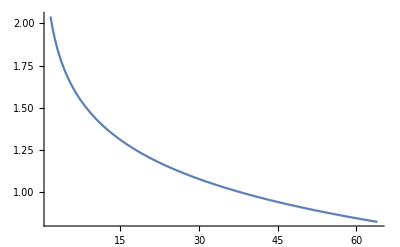

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

1.57728

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

1.10121

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

2.71739 z^2-1.73337 z^3

```mathematica
(* 
sqrt(s)=15.1047 GeV sigma(PP)=2.6797 fb-1.7509 fb,
sqrt(s)=22.6047 GeV sigma(PP)=1.7853 fb-0.1139 fb
sqrt(s)=27.6047 GeV sigma(PP)=0.7875 fb-0.0551 fb
*)
```